# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Desktop\\Diagonalization test\\QMB_offline.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

# Diagonalization one

```mathematica
L=14;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
h=1;
g=0.5;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

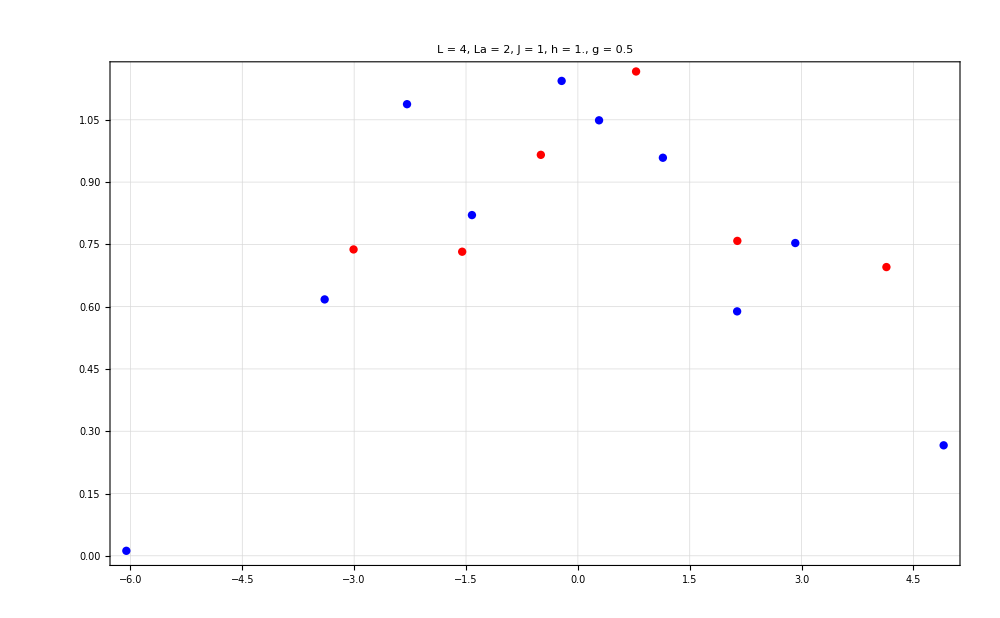

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

# Diagonalization two

```mathematica
PositiveParitySubspaceBasis[L_]:=DeleteDuplicatesBy[Tuples[{0,1},L],First[Sort[{#,Reverse[#]}]]&];
```

```mathematica
base = PositiveParitySubspaceBasis[L];
tagsbase = Tag /@ base;
```

```mathematica
(*Esto seguro se puede optimizar, pero queda para después*)
Hx = Module[{m, dimSubspace = Length[tagsbase], q, l, tmp1},
m = SparseArray[Prepend[
	Table[
		(* Encontrar estados \sum_j \dyad{0}{1}_j \ket{k} *)
		tmp1 = Select[Join[ConstantArray[j,L]-IdentityMatrix[L],If[PalindromeQ[j],{},ConstantArray[Reverse[j],L]-IdentityMatrix[L]]], And@@NonNegative[#]&];
		q = ReplaceAll[PalindromeQ[j],{True->0,False->1}];
		(* Encontrar la posición en la base y asignar un valor *)
		Total[
			Table[
				l=ReplaceAll[PalindromeQ[k], {True->0, False->1}];
				SparseArray[Flatten[Position[tagsbase, If[MemberQ[tagsbase, Tag[k]], Tag[k], Tag[Reverse[k]]]]]-> 2.^(-(q+l)/2), dimSubspace]
		, {k, tmp1}]
		]
	,{j,base[[2;;]]}]
	,SparseArray[{},dimSubspace]
	]
	];
Transpose[m]+m
];
```

$Aborted

```mathematica
Hz=DiagonalMatrix[Total[(-1)^#]&/@base, TargetStructure->"Sparse"];
JJ=DiagonalMatrix[Total[(-1)^Differences[#]]&/@base, TargetStructure->"Sparse"];
Hamiltonian[hx_,hz_,J_]:=-hx*Hx-hz*Hz-J*JJ;
```

```mathematica
hx=1;
J=1;
hz=0.5;
```

```mathematica
Sort[Eigenvalues[Hamiltonian[hx,hz,J]]]
```

{-6.05477,-3.39547,-2.29103,-1.42045,-0.217772,0.283935,1.13996,2.13547,2.91528,4.90485}

```mathematica
eveneigenval
```

{-6.05477,-3.39547,-2.29103,-1.42045,-0.217772,0.283935,1.13996,2.13547,2.91528,4.90485}

```mathematica
{eigenval1,eigenvec1}=Transpose[Sort[Transpose[Eigensystem[Heven]]]];
{eigenval2,eigenvec2}=Transpose[Sort[Transpose[Eigensystem[Hamiltonian[hx,hz,J]]]]];
```

```mathematica
eigenval1
eigenval2
```

{-6.05477,-3.39547,-2.29103,-1.42045,-0.217772,0.283935,1.13996,2.13547,2.91528,4.90485}

{-6.05477,-3.39547,-2.29103,-1.42045,-0.217772,0.283935,1.13996,2.13547,2.91528,4.90485}

```mathematica
Table[Chop[Abs[Conjugate[i].j]^2],{i,eigenvec1},{j,eigenvec2}]//MatrixForm
```

(0.882598 | 0.00834657 | 0.00495211 | 0.00163007 | 0.0371353 | 0.0332686 | 0.0184299 | 0.00178474 | 0.00425776 | 0.0075969
0.00343168 | 0.898912 | 0.0162468 | 0.00704855 | 0.00275042 | 0.0384141 | 0.0192198 | 0.00683702 | 0.000106335 | 0.00703336
0.063824 | 0.0227292 | 0.0110089 | 0.31596 | 0.11111 | 0.155057 | 0.058449 | 0.00626073 | 0.000402919 | 0.255198
0.00838854 | 0.00282675 | 0.0866983 | 0.24578 | 0.204566 | 0.0870663 | 0.00144856 | 0.0382893 | 0.00460588 | 0.32033
0.00671504 | 0.00169941 | 0.0308608 | 0.241077 | 0.0626832 | 0.290203 | 0.211643 | 0.00814044 | 0.144475 | 0.00250267
0.025292 | 0.0102458 | 0.240572 | 0.00645461 | 0.250376 | 0.017067 | 0.0615718 | 0.000760186 | 0.0585719 | 0.32909
0.00348189 | 0.0484998 | 0.0111534 | 0.00807854 | 0.0298444 | 0.194642 | 0.249109 | 0.392051 | 0.0417565 | 0.0213834
0.00418079 | 9.23206×10^-6 | 0.0769527 | 0.00660066 | 0.0577238 | 0.000585767 | 0.198289 | 0.296535 | 0.357757 | 0.00136699
0.00208799 | 0.0067235 | 0.0503908 | 0.119621 | 0.0115227 | 0.151886 | 0.101937 | 0.243976 | 0.311662 | 0.000193065
9.42397×10^-8 | 7.71399×10^-6 | 0.471165 | 0.0477496 | 0.232288 | 0.0318099 | 0.0799031 | 0.00536613 | 0.0764046 | 0.0553059)

```mathematica
PositiveParitySubspaceBasis[L]
```

{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,1},{1,0,1,1},{1,1,1,1}}

```mathematica
evenBasis//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

# Diagonalization three

```mathematica
HxTotal[vec_, L_] := BitFlip[vec, #]& /@ Range[0,L-1];

TotalSigmaX = Total[Pauli /@ IdentityMatrix[L]];
(* Elemento representativo de los elementos de la base impar. Por ej, {0,1} para el estado 1/Sqrt[2](|01⟩+|10⟩) *)
repElementOddBasis = DeleteDuplicatesBy[Select[Tuples[{0, 1}, L], # != Reverse[#]&], First[Sort[{#,Reverse[#]}]]&];
(* Reglas de asignacion, por terminar de pulir *)
rulesCompToSymm = Join[Thread[Flatten[{FromDigits[#, 2],FromDigits[Reverse[#], 2]}&/@repElementOddBasis]-> Flatten[Transpose[ConstantArray[Range[Length[repElementOddBasis]], 2]]]],Thread[Complement[Range[0,2^L-1],Flatten[{FromDigits[#, 2],FromDigits[Reverse[#], 2]}&/@repElementOddBasis]]->Nothing]];
rulesSymmToComp = Thread[Range[Length[repElementOddBasis]]->({FromDigits[#,2],FromDigits[Reverse[#],2]}&/@repElementOddBasis)];
rules = Thread[Complement[Range[0,2^L-1],Flatten[{FromDigits[#, 2],FromDigits[Reverse[#], 2]}&/@repElementOddBasis]]->Nothing];
dimHodd = Length[repElementOddBasis];
rules2 = Join[Flatten[{FromDigits[#,2] -> {FromDigits[#,2],FromDigits[Reverse[#],2]}, FromDigits[Reverse[#],2] -> {FromDigits[#,2],FromDigits[Reverse[#],2]}}&/@repElementOddBasis,1],rules];

TotalSigmaXOdd = SparseArray[
Flatten[
Table[
	With[{vec = i /. rulesSymmToComp},
		{ReplaceAll[{vec[[1]], #[[1]]}, rulesCompToSymm] -> (1/2)*Total[{1., -1., -1., 1.}*(TotalSigmaX[[#1, #2]] &@@@ Tuples[{vec, #} + 1])]}& /@ ReplaceAll[Select[HxTotal[vec[[1]], L], ReplaceAll[#, rulesCompToSymm] > i&], rules2]
	]
, {i, dimHodd - 1}]
, 2]
, {Length[repElementOddBasis], Length[repElementOddBasis]}];
TotalSigmaXOdd = TotalSigmaXOdd + ConjugateTranspose[TotalSigmaXOdd];
```

```mathematica
Clear[Hamiltonian];
TotalSigmaZOdd = DiagonalMatrix[Total[(-1)^#]&/@repElementOddBasis, TargetStructure->"Sparse"];
TotalSigmaZNNodd = DiagonalMatrix[Total[(-1)^Differences[#]]&/@repElementOddBasis, TargetStructure->"Sparse"];
Hamiltonian[hx_, hz_, J_] := -hx*TotalSigmaXOdd - hz*TotalSigmaZOdd - J*TotalSigmaZNNodd;
```

```mathematica
{eigenval1,eigenvec1}=Transpose[Sort[Transpose[Eigensystem[Hodd]]]];
{eigenval2,eigenvec2}=Transpose[Sort[Transpose[Eigensystem[Hamiltonian[hx,hz,J]]]]];
```

```mathematica
eigenval1
eigenval2
```

{-3.00796,-1.55144,-0.496596,0.780429,2.13824,4.13733}

{-3.00796,-1.55144,-0.496596,0.780429,2.13824,4.13733}

```mathematica
Table[Chop[Abs[Conjugate[i].j]^2],{i,eigenvec1},{j,eigenvec2}]//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 1.)